```mathematica
ME 454  Final Project: Optimal Control of Kinematic Car Motion While Avoiding Obstacle | Abhishek Patil and Tanay Choudhary
```

```mathematica
(* Cell #1: Quit current Kernal *)
Quit[]
```

```mathematica
(* Cell #2: Opens communication with iRobot Create and Define some helpful functions for iRobot Create communication*)
tc[n_,bits_:32]:=If[n≥0,IntegerDigits[n,2,bits],1-IntegerDigits[2^bits-n+1,2,bits]] (*two's complement*)
tc2dec[n_]:={FromDigits[n[[1;;8]],2],FromDigits[n[[9;;16]],2]}
drive[dev0_,un_]:=Module[{utc,udec},
utc = {tc[un[[1]],16] ,tc[un[[2]],16]};
udec = Join[tc2dec[utc[[1]]],tc2dec[utc[[2]]]];
DeviceWrite[dev0,Join[{145},udec]];
];
(* Apple/Linux*)
room=DeviceOpen["Serial",{"/dev/ttyUSB0","BaudRate"->115200}]
(* Windows *)
(*room=dev=DeviceOpen["Serial",{"COM4","BaudRate"->115200}]*)
start=128;
fullMode=132;
safeMode=131;
clean=135;
max=136;
spot=134;
powerdown=133;
reset=7;
stop=173;
park={137,0,0,0,0};
DeviceWrite[room,start]; 
DeviceWrite[room,fullMode]; 
Pause[0.01]
DeviceWrite[room,{164, 72, 73, 94, 94}];
DeviceWrite[room,{139,0,0,255}];
```

DeviceObject[…]

```mathematica
Quit[];
```

```mathematica
(* Cell #3: iLQR*)
(* Define variables,dynamics,and initial conditions *)
(*States, Inputs, Desired Trajectory*)
q = {x[t],y[t],θ[t],v1[t],v2[t]};
qdot = D[q,t]; 
u = {ul,ur};
qd = {t/5,0.001,0,0,0};
qdT={3.,0,0,0,0};
obsxy={1.,0};
obsxy2={2.,0};

(*Dynamics*)
f[u_]:={0.001*0.5*(q[[4]]+q[[5]])*Cos[q[[3]]],0.001*0.5*(q[[4]]+q[[5]])*Sin[q[[3]]],0.001*(q[[4]]-q[[5]])/(0.235),15*(u[[1]]-q[[4]]),15*(u[[2]]-q[[5]])}
A = D[f[u],{q}];
B = D[f[u],{u}];

(*IC*)
u0 = {50.,50.};
q0 = {0.,0.,0.,0.,0.};
initCon = Thread[(q/. t-> t0)== q0];

t0 = 0.;
tf =30.;
initSol = NDSolve[Join[Thread[qdot== f[u0]],initCon],q[[;;,0]],{t,t0,tf}];
ξ[0] = {initSol[[1]],Thread[u-> u0]};

(*Cost*)
R=0.0001*IdentityMatrix[Length@u];
Q=0.001*IdentityMatrix[Length@q];
Q[[3,3]] = 0;
Q[[4,4]] = 0;
Q[[5,5]] = 0;
(*TERMINAL CONDITION MATTERS A LOT*)
P1=10000*IdentityMatrix[Length@q]; 
P1[[3,3]] = 0;
P1[[4,4]] = 0;
P1[[5,5]] = 0;
obsW=1; (*AVOIDING OBSTACLES IS ALSO IMPORTANT*)

(* Simulate System *)
forwardSim[t00_,tff_,contr_]:= NDSolve[Join[Thread[qdot== f[contr]],initCon],q[[;;,0]],{t,t0,tf}];

(* Variable Definitions*)
Z = Table[z[i][t],{i,1,Length@q}];
dZ = D[Z,t];
zinit = Thread[(Z/.t-> 0)== ConstantArray[0,Length@q]];
Ps = Table[P[i,j][t],{i,1,Length@q},{j,1,Length@q}];
dPs = D[Ps,t];
(*Pinit = Thread[Flatten@(Ps/.t-> tf)== Flatten@(0*IdentityMatrix[Length@q])];*)
Pinit = Thread[Flatten@(Ps/.t-> tf)== Flatten@P1];
rs = Table[r[i][t],{i,1,Length@q}];
drs = D[rs,t];
(*rinit = Thread[Flatten@(rs/.t-> tf)== ConstantArray[0,Length@q]];*)
rinit[ξ0_]:= Thread[Flatten@(rs/.t-> tf)== P1.((q/.forwardSim[t0,tf,u/.ξ0[[2]]]/.t->tf)[[1]]-(qdT))];

(* Compute Cost: ADDED TERMS FOR TERMINAL CONDITION AND BARRIER FUNCTIONS FOR OBSTACLES *)
calcCost[ξ0_]:=NIntegrate[0.5*(q-qd).Q.(q-qd)/.Flatten@ξ0,{t,t0,tf},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->False}]+

NIntegrate[0.5*u.R.u/.Flatten@ξ0,{t,t0,tf},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->False}]+

0.5*(((q/.forwardSim[t0,tf,u/.ξ0[[2]]]/.t->tf)[[1]]-(qdT)).P1.((q/.forwardSim[t0,tf,u/.ξ0[[2]]]/.t->tf)[[1]]-(qdT)))+

NIntegrate[(obsW*Abs@Log[Abs[(q[[1]]-obsxy[[1]])^2+(q[[2]]-obsxy[[2]])^2-0.225]])/.Flatten@ξ0,{t,t0,tf},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->False}]+

NIntegrate[(obsW*Abs@Log[Abs[(q[[1]]-obsxy2[[1]])^2+(q[[2]]-obsxy2[[2]])^2-0.225]])/.Flatten@ξ0,{t,t0,tf},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->False}];

(* Computed dJ *)
dJ[at0_,bt0_,ζ0_]:=NIntegrate[at0.ζ0[[1]]+bt0.ζ0[[2]],{t,t0,tf},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->False}]
(* Saturate Input *)
sat[un_]:=If[Abs[un]>500 , Sign[un]*500,un];
(* Compute Descent Direction *)
descDir[ξ0_,At_,Bt_,at_,bt_]:=Module[{ricsol,Psol,rsol,v,zeq,zsol,c},
ricsol = solveRic[ξ0,At,Bt,at,bt,R,Q];
Psol = ricsol[[1]];
rsol = ricsol[[2]];
v = -Inverse[R].(bt+Btᵀ.Psol.Z+Btᵀ.rsol);
zeq = Thread[dZ== At.Z+Bt.v];
zsol = NDSolve[Join[zeq,zinit],Z[[;;,0]],{t,t0,tf}];
c = Table[ListInterpolation[Table[v[[iter]]/.zsol[[1]],{t,t0,tf,0.01}],{{t0,tf}}][t],{iter,1,Length@v}];
Return[{Z/.zsol[[1]],c}]
]
(* Solve Riccati Equations *)
solveRic[ξ0_,A0_,B0_,a0_,b0_,R0_,Q0_]:=Module[{Peq,eq1,eq2,req,sol,Psol,rsol},
Peq = -(A0ᵀ.Ps + Ps.A0 - Ps.B0.Inverse[R0].B0ᵀ.Ps+Q0);
eq1 = Thread[Flatten@dPs == Flatten@Peq];
req = -((A0-B0.Inverse[R0].B0ᵀ.Ps)ᵀ.rs+a0-Ps.B0.Inverse[R0].b0);
eq2 = Thread[Flatten@drs== Flatten@req];
sol = NDSolve[Join[eq1,eq2,Pinit,rinit[ξ0]],Join[(Flatten@Ps)[[;;,0]],rs[[;;,0]] ],{t,t0,tf}];
(*sol = NDSolve[Join[eq1,eq2,Pinit,rinit],Join[(Flatten@Ps)[[;;,0]],rs[[;;,0]] ],{t,t0,tf}];*)
Psol = Ps/.sol[[1]];
rsol = rs/.sol[[1]];
Return[{Psol,rsol}]
]
(* Update trajectory along Descent Direction *)
updatetrajectory[ξ0_,ζ0_,γ0_] := Module[{ricsol,an,bn,infx,infu,K,sol,contr,c},
contr  = (u/.ξ0[[2]])+γ0*ζ0[[2]];
contr = {sat[contr[[1]]],sat[contr[[2]]]};
sol = forwardSim[t0,tf,contr];
c = Table[ListInterpolation[Table[contr[[iter]]/.sol[[1]],{t,t0,tf,0.01}],{{t0,tf}}][t],{iter,1,Length@contr}];
Return[{sol[[1]],Thread[u-> c]}]
]

(*Debugging Information*)
Print["Iteration : ",Dynamic@i];
Print["J: ",Dynamic[J]];
Print["dj mag: ", Dynamic[Abs[dj]]];
Print["armijo: ",Dynamic@j];
Print[Dynamic@ParametricPlot[{q[[1;;2]]/.ξ[i][[1]],{qdT[[1]]+0.3*Sin[t],qdT[[2]]+0.3Cos[t]},{obsxy[[1]]+0.1*Sin[t],obsxy[[2]]+0.1Cos[t]},{obsxy2[[1]]+0.1*Sin[t],obsxy2[[2]]+0.1Cos[t]}},{t,t0,tf},PlotRange->Full]];

(* Line Search Parameters *)
β = 0.25;tol = 0.0001;α = 0.001;armmax = 25;

i = 0;
(*Max iLQR iterations*)
imax = 11;

(*iLQR Loop*)
While[i<imax,
At = A/.Flatten@ξ[i];
Bt = B/.Flatten@ξ[i];
at = Q.((q-qd)/.ξ[i][[1]]);
bt = R.(u/.ξ[i][[2]]);
ζ[i]=descDir[ξ[i],At,Bt,at,bt];
γ=β;
ξnew=updatetrajectory[ξ[i],ζ[i],γ];

dj = dJ[at,bt,ζ[i]];
If[Abs[dj]<tol,Break[]];

J = calcCost[ξ[i]];
Jar = J+α*γ*dj;
JP = calcCost[ξnew];
j = 1;

While[JP>Jar,
If[j>armmax ,Break[]];
γ = β^j;
ξnew=updatetrajectory[ξ[i],ζ[i],γ];
JP = calcCost[ξnew];
Jar = J+α*γ*dj;
j= j + 1;
];
If[JP<Jar,ξ[i+1] = ξnew;,Break[]];
i++;
];
```

Iteration :

J:

dj mag:

armijo:

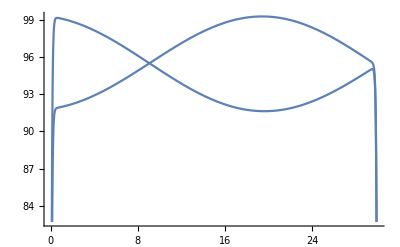

```mathematica
(*Cell #4: Debugging Plots*)
(* Plot optimized trajectory and controls *)
anim=ListAnimate[Table[ParametricPlot[{q[[1;;2]]/.ξ[s][[1]],{qdT[[1]]+0.3*Sin[t],qdT[[2]]+0.3Cos[t]},{obsxy[[1]]+0.1*Sin[t],obsxy[[2]]+0.1Cos[t]},{obsxy2[[1]]+0.1*Sin[t],obsxy2[[2]]+0.1Cos[t]}},{t,t0,tf},PlotRange->Full],{s,1,11}]]
(* Plot optimized inputs *)
Plot[q[[4;;5]]/.ξ[11][[1]],{t,t0,tf},PlotLegends->"ul,ur"]
```

```mathematica
(* Cell #5: Sends the Optimized Control Commands to the Romba*)
control =q[[4;;5]]/.ξ[11][[1]]
tt = 0;
dt = 0.1;
While[tt<tf,
input = (control/.t-> (tt+dt/2));
inputi = IntegerPart[input];
drive[room,inputi];
tt = tt + dt;
Pause[dt];
]
DeviceWrite[room,park]
```

```mathematica
(* Cell #6: Release control of the iRobot Create and close communication link properly*)
DeviceWrite[room,stop]; 
DeviceClose[room];
```